Sam Dolan, February 2024.
Code to read, manipulate and plot the data for the metric perturbations that was calculated and exported by metric_reconstruction_calc_radiative.nb.
In “1D plotting” I examine the radial functions, and check that the values at r=r0 are regularizable according to a power law in (l+1/2). 
In “Validation against time-domain 2+1D data”, I compare with some earlier results from my time-domain code (Dolan and Barack).
With thanks to Patrick Bourg for code testing, and Barry Wardell for code in the Barack-Lousto section.

```mathematica
ClearAll["Global`*"]
fontsize=14;
SetOptions[Plot,BaseStyle->FontSize->fontsize];
SetOptions[ListPlot,BaseStyle->FontSize->fontsize];
SetOptions[ListLogPlot,BaseStyle->FontSize->fontsize];
SetOptions[ListLogLogPlot,BaseStyle->FontSize->fontsize];
<<SpinWeightedSpheroidalHarmonics`
```

```mathematica
(* Choose the parameter file. *)
(* Set 1: lower resolution, smaller domain, lmax = 20. *)
iConfig="99-060-002"; 
(* Set 2: higher resolution, larger domain, lmax = 30. *)
```

## Preliminaries

### Metric and tetrad

```mathematica
ρ=r+I*a*Cos[θ];
ρc=r-I*a*Cos[θ];
Σ=ρ*ρc;
Δsubs={Δ[r]->r^2-2*M*r+a^2,Δ'[r]->2*(r-M),Δ''[r]->2,Δ'''[r]->0};
Ksubs={K[r]->ω*(r^2+a^2)-a*m,K'[r]-> 2*ω*r,K''[r]->2*ω,K'''[r]->0};
ΔKsubs=Join[Δsubs,Ksubs];
ΔKsimp={Δ'[r]->2*(r-M),Δ''[r]->2,Δ'''[r]->0,K'[r]-> 2*ω*r,K''[r]->2*ω,K'''[r]->0};
QQ=m/Sin[θ]-a*ω*Sin[θ];
a0subs={a->0};
Dop[n_,R_]:=D[R,r]-I*K[r]/Δ[r]*R+n*Δ'[r]/Δ[r]*R;
Ddag[n_,R_]:=D[R,r]+I*K[r]/Δ[r]*R+n*Δ'[r]/Δ[r]*R;
Lop[n_,R_]:=D[R,θ]+QQ*R+n*Cot[θ]*R;
Ldag[n_,R_]:=D[R,θ]-QQ*R+n*Cot[θ]*R;
Dop[R_]:=Dop[0,R];
Ddag[R_]:=Ddag[0,R];
Lop[R_]:=Lop[0,R];
Ldag[R_]:=Ldag[0,R];
```

```mathematica
(* Inverse metric *)
lp={(r^2+a^2)/Δ[r],1,0,a/Δ[r]};
lm={-(r^2+a^2)/Δ[r],1,0,-a/Δ[r]};
mp={I*a*Sin[θ],0,1,I/Sin[θ]};
mm={-I*a*Sin[θ],0,1,-I/Sin[θ]};
gup=Table[1/(2*Σ)*(Δ[r]*(lp[[i]]*lm[[j]]+lm[[i]]*lp[[j]])+mp[[i]]*mm[[j]]+mm[[i]]*mp[[j]]),{i,1,4},{j,1,4}];
Simplify[Det[gup]+1/(Σ^2*Sin[θ]^2)]
tmp=gup.{-EE,0,0,LL}/.{θ->π/2}//Simplify;
utsubs={ut->tmp[[1]]};
```

0

```mathematica
(* Important information. 
The variables used in the m-mode code are related to the components of hbar, in the following way:
 hbar[ind[i]] = 1/r α[i] u[i] e^{im \tilde{ϕ}}. 
Here the indices are in the order given below, along with the factors of α.
I have inferred this from the (2010/11) codes:  
   wave_eq_grtensor.txt
  and Code/Maple/grtensor2/hbar_kerr_trqp_rprm.mpl
*)
ϕtilde=ϕ+a/(rp-rm)*Log[(r-rp)/(r-rm)];
indexorder={{0,0},{0,1},{0,2},{0,3},{1,1},{1,2},{1,3},{2,2},{2,3},{3,3}};
αs={1,r/(r-rp),r,r*Sin[θ],r^2/(r-rp)^2,r^2/(r-rp),r^2*Sin[θ]/(r-rp),r^2,r^2*Sin[θ],r^2*Sin[θ]^2};
```

```mathematica
(* Verify that this is what has been implemented, by calculating the trace, and then comparing with the expression in the C code. *)
indmap={{1,1}->1,{1,2}->2,{2,1}->2,{1,3}->3,{3,1}->3,{1,4}->4,{4,1}->4,{2,2}->5,{2,3}->6,{3,2}->6,{2,4}->7,{4,2}->7,{3,3}->8,{3,4}->9,{4,3}->9,{4,4}->10};
hbar=(1/r)*Table[αs[[ {i,j}/.indmap]]*u[({i,j}/.indmap)-1],{i,1,4},{j,1,4}];
trace1=-Tr[hbar.gup]//Simplify;
traceco=Table[Simplify[Coefficient[trace1,u[k]]],{k,0,9}];
(* Compare this with the coefficients in flux.cpp in the calc_trace() function. *)
codeco={(r^4+(a*r)^2+(a*r*Cos[θ])^2-2*r*(a*Cos[θ])^2+2*a^2*r+a^4*Cos[θ]^2)/(Δ[r]*r*Σ),0,0,4*r*a*Sin[θ]/(Δ[r]*Σ),-r*Δ[r]/((r-rp)^2*Σ),0,0,-r/Σ,0,-r*(Σ-2*r)/(Δ[r]*Σ)};
Simplify[(traceco-codeco)/.Δsubs/.{M->1}]
(* OK, verified. *)
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
(* Sometimes it is convenient to work with the projections of the metric perturbation hbar on to the null tetrad. *)
hcomp=Simplify[{hbar.lp.lp, hbar.lm.lm,hbar.mp.mp,hbar.mm.mm,ρ*hbar.lp.mp,ρc*hbar.lp.mm,ρc*hbar.lm.mp,ρ*hbar.lm.mm,Σ*(-hbar.mp.mm),-(Δ[r]*hbar.lp.lm+hbar.mp.mm)/Σ}/.{ρ->r+I*a*Cos[θ],ρc->r-I*a*Cos[θ]}]/.{Cos[2θ]->2*Cos[θ]^2-1};
(hcomp[[10]]-trace1)//Simplify
```

0

```mathematica
(* If you want to plot the u variables, you will need to run the commented code. *)
(*
htetrad=Table[htet[qi],{qi,1,10}];
eqs=Table[htetrad[[i]]==hcomp[[i]],{i,1,10}]//Simplify;
eqsol=Solve[eqs,Table[u[i],{i,0,9}]];
htettou=Simplify[eqsol[[1]] ,Assumptions->θ>0&&θ<π]
*)
```

### Import config file

```mathematica
(* Read the parameters from a configuration file *)
(* Read the Configuration parameters *)
filepath=NotebookDirectory[]<>"config/";
filen=filepath<>"config"<>ToString[iConfig]<>".txt";
s=Import[filen,"String"];
s1=StringSplit[s,"\n"];
stmp=Map[StringSplit[#,"\t"]&,s1];
(* Handle the case where spaces were used in place of tabs **)
altsplit[s_]:={First[#],Last[#]}&@StringSplit[s," "];
s2=Map[If[Length[#]<2,altsplit[#[[1]]],#]&,stmp];
configparams=Map[{#[[1]],ToExpression[#[[2]]]}&,s2];
GetParam[key_]:=Module[{ls,val},
ls=Select[configparams,#[[1]]==key&];
If[Length[ls]>0,
val=ls[[1]][[2]];
If[ NumericQ[val]&&(!(IntegerQ[val])),val=SetPrecision[val,prec]];
,
val=Null
];
val
];
GetParam[key_,default_]:=If[GetParam[key]===Null,default,GetParam[key]];
```

```mathematica
(* Read in the numerical parameters. *)
prec=GetParam["prec",32]; (* Number of digits to use where required. *)
iround=1000;
a0=SetPrecision[Round[GetParam["a"]*iround]/iround,prec];
r0=SetPrecision[Round[GetParam["r0"]*iround]/iround,prec];
mm=GetParam["m"];
lmax=GetParam["lmax"];
lplot=GetParam["lplot"];
dformat=ToString@GetParam["dformat","Real64"];
{a0,r0,mm,lmax,lplot,dformat}
```

{0.99,6.,2,20,14,Real64}

```mathematica
Ω0=1/(Sqrt[r0^3]+a0);
ω0=mm*Ω0;
aω0=If[a0==0,0,a0*ω0];
ΔKr0subs=Map[#[[1]]->(#[[2]]/.{a->a0,r->r0,M->1,m->mm,ω->ω0})&,Join[Δsubs,Ksubs]];
awsubs=Join[SetPrecision[{a->a0,ω->ω0},prec],{m->mm,M->1}];
lmins0=Abs[mm];
lmins1=Max[1,Abs[mm]];
lmins2=Max[2,Abs[mm]];
lmins={lmins2,lmins1,lmins0,lmins1,lmins2};
rprmvals={rp->1+Sqrt[1-a^2],rm->1-Sqrt[1-a^2]}/.awsubs;
```

### Import lm data

```mathematica
(* Read in the r and r* values. *)
tmp=Import[NotebookDirectory[]<>"data/lm_rsL_"<>ToString[iConfig]<>".dat"];
{rstarsL,rsL}=Transpose[tmp];
tmp=Import[NotebookDirectory[]<>"data/lm_rsR_"<>ToString[iConfig]<>".dat"];
{rstarsR,rsR}=Transpose[tmp];
rstarmin=Last[rstarsL]
rstarmax=Last[rstarsR]
Length[rstarsL]+Length[rstarsR]
```

-19.818321037279361410613334121178331

99.931678962720638589386665878821669

481

```mathematica
(* Read in the lm-mode data from the binary files, and put this in the most convenient form for plotting. *)
fn=NotebookDirectory[]<>"data/lm_in_"<>ToString[iConfig]<>".bin"
dataL=Import[fn,dformat];
dimsL={Length[rsL],20,lmax+1}
GetIndexL[ri_,qi_,ll_]:=(ri-1)*dimsL[[2]]*dimsL[[3]]+(qi-1)*dimsL[[3]]+ll+1;
compL=Table[dataL[[GetIndexL[ri,qi,ll]]]+I*dataL[[GetIndexL[ri,qi+10,ll]]],{ll,0,lmax},{qi,1,10},{ri,1,Length[rsL]}] ;

fn=NotebookDirectory[]<>"data/lm_up_"<>ToString[iConfig]<>".bin"
dataR=Import[fn,dformat];
dimsR={Length[rsR],20,lmax+1}
GetIndexR[ri_,qi_,ll_]:=(ri-1)*dimsR[[2]]*dimsR[[3]]+(qi-1)*dimsR[[3]]+ll+1;
compR=Table[dataR[[GetIndexR[ri,qi,ll]]]+I*dataR[[GetIndexR[ri,qi+10,ll]]],{ll,0,lmax},{qi,1,10},{ri,1,Length[rsR]}] ;
```

/Users/sm1srd/Code/KerrLorenzCirc/data/lm_in_99-060-002.bin

{110,20,21}

/Users/sm1srd/Code/KerrLorenzCirc/data/lm_up_99-060-002.bin

{371,20,21}

```mathematica
If[mm!=0,
(* Now also read in the s=2, s=1 and s=0 parts. *)
For[ss=2,ss>=0,ss--,
fn=NotebookDirectory[]<>"data/lm_in_s"<>ToString[ss]<>"_"<>ToString[iConfig]<>".bin";
dataL=Import[fn,dformat];
compLspin[ss]=Table[dataL[[GetIndexL[ri,qi,ll]]]+I*dataL[[GetIndexL[ri,qi+10,ll]]],{ll,0,lmax},{qi,1,10},{ri,1,Length[rsL]}] ;
fn=NotebookDirectory[]<>"data/lm_up_s"<>ToString[ss]<>"_"<>ToString[iConfig]<>".bin";
dataR=Import[fn,dformat];
compRspin[ss]=Table[dataR[[GetIndexR[ri,qi,ll]]]+I*dataR[[GetIndexR[ri,qi+10,ll]]],{ll,0,lmax},{qi,1,10},{ri,1,Length[rsR]}] ;
]
]
```

## 1D plotting

### Radial plots and regularization

```mathematica
(* Apply some radial scalings so that the individual components plotted behave nicely in the near-horizon and far-field. *)
normfacs={Δ[r]^2/r^3,Δ[r]^2/r^3,1/r,1/r,Δ[r]/r^3,Δ[r]/r^3,Δ[r]/r^3,Δ[r]/r^3,1/r^3,r}/.Δsubs/.awsubs;
normsL=Transpose@Table[normfacs/.Δsubs/.{r->rsL[[ri]]},{ri,1,Length[rsL]}];
normsR=Transpose@Table[normfacs/.Δsubs/.{r->rsR[[ri]]},{ri,1,Length[rsR]}];
```

1. Select a component of the metric perturbation (icomp = 1 to 10) and plot the (absolute value of) the radial function for all ell across the domain in r*.
You should see clear exponential convergence with l except in the region near from r=r0. 
The l=|m| mode is dominant in the far-field (r*>>M) and near the horizon (r* negative region).

```mathematica
icomp=3; 
fig1=ListLogPlot[Join[Table[Transpose@{rstarsL,Abs[normsL[[icomp]]*compL[[ll+1,icomp]]]},{ll,Abs[mm],lplot}],Table[Transpose@{rstarsR,Abs[normsR[[icomp]]*compR[[ll+1,icomp]]]},{ll,Abs[mm],lplot}]],PlotRange->All,AxesLabel->{"r*/M","Abs(h_AB)"},ImageSize->Large,Joined->True,PlotLabels->Join[Table[None,{ll,Abs[mm],lplot}],Table["l = "<>ToString[ll],{ll,Abs[mm],lplot}]]]
```

-Graphics-

2. At r = r0, the modes should go like (l + 1/2)^(-1) [for component 1 at least], whereas the individual spin parts diverge as (l + 1/2)^3. In other words, we are relying on a delicate cancellation in this calculation. 
If the sum starts to deviate away from (l + 1/2)^(-1), this is indicative of a loss of accuracy in the high - ell modes, and you should adjust the internal parameters accordingly, or lower “lplot” to exclude these modes.

```mathematica
(* Inspect the relative contribution of spin-2, spin-1, spin-0 on the worldline as a function of ll *)
lvals=Table[ll+1/2,{ll,Abs[mm],lmax}];
ri=1;
SetOptions[ListLogLogPlot,BaseStyle->FontSize->14];
If[mm!=0,
fig2a=ListLogLogPlot[{Transpose@{lvals,Abs@compR[[Abs[mm]+1;;,icomp,ri]]},Transpose@{lvals,Abs@compRspin[2][[Abs[mm]+1;;,icomp,ri]]},Transpose@{lvals,Abs@compRspin[1][[Abs[mm]+1;;,icomp,ri]]},Transpose@{lvals,Abs@compRspin[0][[Abs[mm]+1;;,icomp,ri]]}},PlotLabels->{"Sum","s=2","s=1","s=0"},PlotLabel->"l modes of h_AB at r = r_0    (r_0= "<>ToString[Round[r0,0.01]]<>"M, a = "<>ToString[Round[a0,0.01]]<>"M, up)",AxesLabel->{"l+1/2","Abs(h_(l + l +))"}];
fig2b=LogLogPlot[{x^3,1/x},{x,2,lmax+1/2},PlotStyle->{Dashed,Dotted}];
,
fig2a=ListLogLogPlot[Transpose@{lvals,Abs@compR[[;;,icomp,ri]]}];
fig2b=LogLogPlot[1/x,{x,2,lmax+1/2},PlotStyle->{Dashed,Dotted}];
];
fig2=Show[fig2a,fig2b,ImageSize->Large]
```

-Graphics-

```mathematica
(*
Export[NotebookDirectory[]<>"data/lmodes_by_radius.pdf",fig1]
Export[NotebookDirectory[]<>"data/lmodes_on_worldline_s012.pdf",fig2]
*)
```

3. Inspect the scaling of the individual spin parts at large r, relative to the sum, for a chosen l.

```mathematica
If[mm!=0,
lval=Abs[mm];  (* Pick a value of l here. *)
ds1=Join[
{Transpose@{rstarsL,Abs[normsL[[icomp]]*compL[[lval+1,icomp]]]}},
{Transpose@{rstarsR,Abs[normsR[[icomp]]*compR[[lval+1,icomp]]]}}
]; 
ds2=Join[
Table[Transpose@{rstarsL,Abs[normsL[[icomp]]*compLspin[ss][[lval+1,icomp]]]},{ss,0,2}],
Table[Transpose@{rstarsR,Abs[normsR[[icomp]]*compRspin[ss][[lval+1,icomp]]]},{ss,0,2}]
];
fig3a=ListLogPlot[ds1,PlotRange->All,AxesLabel->{"r*/M","Abs"},ImageSize->Large,Joined->True,PlotStyle->{{Blue,Thickness[.004]}},PlotLabels->{None,"Sum"},ImageSize->Large];
fig3b=ListLogPlot[ds2,PlotRange->All,AxesLabel->{"r*/M","Abs"},ImageSize->Large,Joined->True,PlotStyle->{{Red,Dashed},{Brown,DotDashed},{Purple,Dotted}},PlotLabels->{None,None,None,"s = 0", "s = 1", "s = 2"}];
fig3=Show[fig3a,fig3b,PlotRange->Automatic]
]
```

-Graphics-

```mathematica
(* Plot again, but just the UP part on a log-log scale. *)
lval=8;
ds1=Transpose@{rstarsR,Abs[normsR[[icomp]]*compR[[lval+1,icomp]]]};
ds2=Table[Transpose@{rstarsR,Abs[normsR[[icomp]]*compRspin[ss][[lval+1,icomp]]]},{ss,0,2}];
fig3a=ListLogLogPlot[ds2,PlotRange->All,FrameLabel->{"r*/M","Abs(h_(l + l +))"},ImageSize->500,Joined->True,PlotStyle->{Red,Brown,Purple},PlotLabels->{"s = 0", "s = 1", "s = 2"},Frame->True,GridLines->Automatic];
fig3b=ListLogLogPlot[ds1,PlotRange->All,AxesLabel->{"r*/M","Abs"},Joined->True,PlotStyle->{{Blue,Thickness[.006]}}];
inds={-4,-1};
fig3c=LogLogPlot[{(x/10)^inds[[1]],(x/10)^inds[[2]]},{x,10,Last@rsR+5},PlotStyle->Dashed];
fig3=Show[fig3a,fig3b,fig3c,PlotRange->Automatic,Epilog->{Text[Style["l = " <> ToString[lval],14] ,Scaled[{0.9,0.9}]]}]
```

-Graphics-

4. More plots, this time on a linear scale.

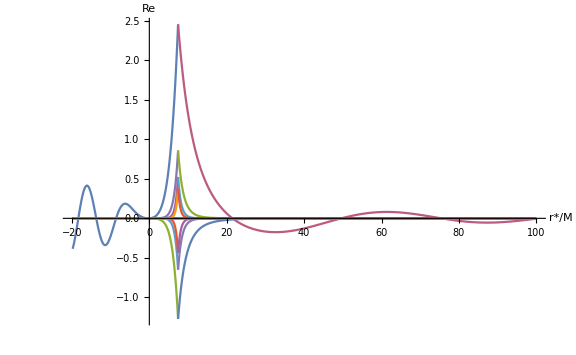

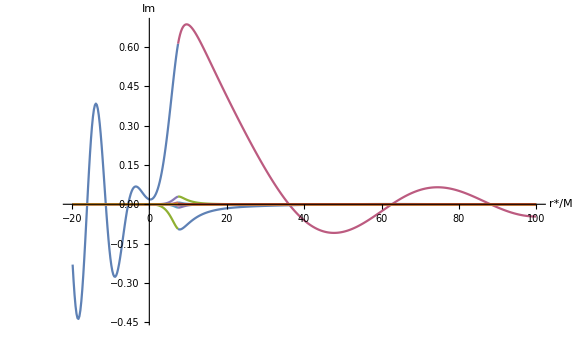

```mathematica
icomp=1; (* Choose the component of the metric perturbation *)
ListPlot[Join[Table[Transpose@{rstarsL,normsL[[icomp]]*Re[compL[[ll+1,icomp]]]},{ll,Abs[mm],lplot}],Table[Transpose@{rstarsR,normsR[[icomp]]*Re[compR[[ll+1,icomp]]]},{ll,Abs[mm],lplot}]],PlotRange->All,AxesLabel->{"r*/M","Re"},ImageSize->Large,Joined->True]
ListPlot[Join[Table[Transpose@{rstarsL,normsL[[icomp]]*Im[compL[[ll+1,icomp]]]},{ll,Abs[mm],lplot}],Table[Transpose@{rstarsR,normsR[[icomp]]*Im[compR[[ll+1,icomp]]]},{ll,Abs[mm],lplot}]],PlotRange->All,AxesLabel->{"r*/M","Im"},ImageSize->Large,Joined->True]
```

### Parity and Barack-Lousto type variables

```mathematica
(* In the Schwarzschild case there is a natural split into even and odd parities. This carries over into the Kerr case. To show this, form combinations inspired by Appendix H of the Kerr-Lorenz-Circ paper (DDKW). 
We should find a nice split into 7 even-parity and 3 odd-parity components. *)
ToBarackLousto[comp_,rval_,ll_]:=Module[{hBL,ff,λhat,Λhat},
ff=Δ[r]/r^2;
λhat=Sqrt[ll*(ll+1)];
Λhat=Sqrt[(ll-1)*ll*(ll+1)*(ll+2)];
hBL=Table[0,{kk,1,10}];
hBL[[1]]=1/2*r*ff^2*(comp[[1]]+comp[[2]])/.Δsubs/.{r->rval};
hBL[[2]]=1/2*r*ff^2*(comp[[1]]-comp[[2]])/.Δsubs/.{r->rval};
hBL[[3]]=(r^4*comp[[10]]-comp[[9]])/r^3/.Δsubs/.{r->rval};
hBL[[4]]=-1/2*ff/r*λhat*(comp[[5]]-comp[[6]]-comp[[7]]+comp[[8]])/.Δsubs/.{r->rval};
hBL[[5]]=-1/2*ff/r*λhat*(comp[[5]]-comp[[6]]+comp[[7]]-comp[[8]])/.Δsubs/.{r->rval};
hBL[[6]]=-(comp[[9]]/r^3)/.Δsubs/.{r->rval};
hBL[[7]]=Λhat/(2*r)*(comp[[3]]+comp[[4]])/.{r->rval};

hBL[[8]]=-I/2*λhat*(Δ[r]/r^2)/r*(comp[[5]]+comp[[6]]-comp[[7]]-comp[[8]])/.Δsubs/.{r->rval};
hBL[[9]]=-I/2*λhat*(Δ[r]/r^2)/r*(comp[[5]]+comp[[6]]+comp[[7]]+comp[[8]])/.Δsubs/.{r->rval};
hBL[[10]]=I*Λhat/(2*r)*(comp[[3]]-comp[[4]])/.{r->rval};

hBL/.awsubs
]
```

```mathematica
(* Note that the last three components are zero for even ll ... *)
ll=2;ri=4;
ToBarackLousto[compR[[ll+1,;;,ri]],rsL[[ri]],ll]
(* ... and the first 7 components are zero for odd ll ... *)
ll=5;ri=4;
ToBarackLousto[compR[[ll+1,;;,ri]],rsL[[ri]],ll]
(* For m=0 only the BL components 1,3,5,6,7 are non-zero for l even, and only the 8 component is non-zero for l odd. *)
```

{1.62195-0.235372 ⅈ,-0.121946+0.720736 ⅈ,3.99606+1.02469 ⅈ,-0.807741+6.38961 ⅈ,-1.89544-2.9239 ⅈ,1.34522+1.00744 ⅈ,-3.74472-6.35024 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

{0.+0. ⅈ,0.+0. ⅈ,0.-2.14767×10^-14 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-2.14767×10^-14 ⅈ,0.+0. ⅈ,2.62195+0.0000793313 ⅈ,0.0000358712+0.147349 ⅈ,-0.000137526+2.23325 ⅈ}

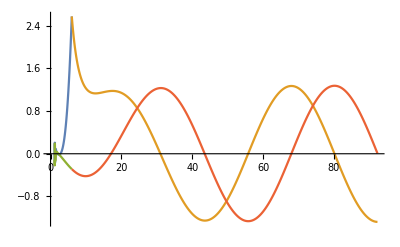

```mathematica
With[{i=1,ll=Abs[mm]},Show[ListLinePlot[{Table[{rsL[[ri]],Re[ToBarackLousto[compL[[ll+1,;;,ri]],rsL[[ri]],ll][[i]]]},{ri,Length[rsL]}],Table[{rsR[[ri]],Re[ToBarackLousto[compR[[ll+1,;;,ri]],rsR[[ri]],ll][[i]]]},{ri,Length[rsR]}],Table[{rsL[[ri]],Im[ToBarackLousto[compL[[ll+1,;;,ri]],rsL[[ri]],ll][[i]]]},{ri,Length[rsL]}],Table[{rsR[[ri]],Im[ToBarackLousto[compR[[ll+1,;;,ri]],rsR[[ri]],ll][[i]]]},{ri,Length[rsR]}]}]]]
```

## 2D plotting

```mathematica
(* Make a 2D grid (r,θ) using a sum over spin-weighted spherical harmonics. *)
nres=GetParam["n",8];
qres=GetParam["angres",8];
qpts=qres*nres+1;
dq=π/(qpts-1);
qs=SetPrecision[Table[dq*kk,{kk,0,qpts-1}],prec];
Ys=Table[If[ll<Max[Abs[ss],Abs[mm]],0,SetPrecision[SpinWeightedSphericalHarmonicY[ss,ll,mm,qs[[kk]],0],prec]],{ss,-2,2},{ll,0,lmax},{kk,1,Length[qs]}];
sws={0,0,2,-2,1,-1,1,-1,0,0};  (* The spin-weights of the 10 components. *)
```

```mathematica
MakeGrid[icomp_,lupper_:lplot]:=Module[{arrL,arrR,arrLsum,arrRsum,arrLR},
(* Choose the component of the MP to plot. *) 
For[ll=Abs[mm],ll<=lplot,ll++,
arrL[ll]=Outer[Times,normsL[[icomp]]*compL[[ll+1,icomp]],Ys[[sws[[icomp]]+3,ll+1]]];
arrR[ll]=Outer[Times,normsR[[icomp]]*compR[[ll+1,icomp]],Ys[[sws[[icomp]]+3,ll+1]]];
];
arrLsum=Sum[arrL[ll],{ll,Abs[mm],lplot}];
arrRsum=Sum[arrR[ll],{ll,Abs[mm],lplot}];
(*ArrayPlot[Transpose@Abs[arrLsum]]
ArrayPlot[Transpose@Abs[arrRsum]]*)
(* Glue the IN and UP solutions together *)
arrLR=Flatten[{Reverse[arrLsum[[2;;]]],arrRsum},1];
arrLR
];
```

```mathematica
arrLR=MakeGrid[1];
Length[arrLR]
Length[rsL]+Length[rsR]-1
```

480

480

```mathematica
ListPlot3D[Transpose@Re[arrLR],AxesLabel->{"θ","r_*",""},ImageSize->500]
ListPlot3D[Transpose@Im[arrLR],AxesLabel->{"θ","r_*",""},ImageSize->500]
(*
ArrayPlot[Transpose@Re[arrLR],ImageSize->Large] (* Real part *)
ArrayPlot[Transpose@Im[arrLR],ImageSize->Large] (* Imaginary part, different scale! *)
*)
```

## Validation against time-domain 2+1D data

```mathematica
filepath=NotebookDirectory[]<>"validation_2+1D/";
i2D=6002;  (* Important: there must be data available with the same parameters as that which you have read in, otherwise there is no hope of success here. *)
```

### Import 2+1D data

```mathematica
(* Read the config file *)
filen=filepath<>"config/config"<>ToString[i2D]<>".txt";
s=Import[filen,"String"];
s1=StringSplit[s,"\n"];
s2=Map[StringSplit[#,"\t"]&,s1];
params2D=Map[{#[[1]],ToExpression[#[[2]]]}&,s2]
Get2DParam[key_]:=Select[params2D,#[[1]]==key&][[1]][[2]];
numpar={a->Get2DParam["a"],r0->Get2DParam["r0"],m->Get2DParam["m"],M->1,rp->1+Sqrt[1-Get2DParam["a"]^2],rm->1-Sqrt[1-Get2DParam["a"]^2],n->Get2DParam["n"],angres->Get2DParam["angres"],twr->Get2DParam["twr"],twq->Get2DParam["twq"]}
(*mtry=m/.numpar*)
```

{{a,0.6},{r0,6.},{m,2},{tmax,250.},{n,12},{angres,8},{twr,24},{twq,12},{nu,0.8},{puncord,4},{gv_opt,2},{glg_opt,0},{ic_opt,0},{ic_ampl,0.}}

{a→0.6,6.→6.,m→2,M→1,rp→1.8,rm→0.2,n→12,angres→8,twr→24,twq→12}

```mathematica
(* Read the parameters *)
filen=filepath<>"data/datadump_params_"<>ToString[i2D]<>".dat";
s=Import[filen,"String"];
s2=StringReplace[StringSplit[s," = "][[2]],"\n"->""];
ns=Map[ToExpression,StringSplit[s2,", "]]
qpts2D=ns[[2]]
rpts2D=ns[[3]];
```

{20,99,2503}

99

```mathematica
(* Read r and θ values *)
filen=filepath<>"data/datadump_rs_"<>ToString[i2D]<>".dat"
rarr2D=Transpose[Import[filen,"Table"]];
rs2D=rarr2D[[1]];
rstars2D=rarr2D[[2]];
filen=filepath<>"data/datadump_qs_"<>ToString[i2D]<>".dat"
qarr2D=Transpose[Import[filen,"Table"]];
qs2D=qarr2D[[1]];
kmid=(Length[qs2D]-1)/2;
```

/Users/sm1srd/Code/KerrLorenz/validation_2+1D/data/datadump_rs_6002.dat

/Users/sm1srd/Code/KerrLorenz/validation_2+1D/data/datadump_qs_6002.dat

```mathematica
(* Read the raw data and the puncture *)
filen=filepath<>"data/datadump_"<>ToString[i2D]<>".bin";
hraw=Import[filen,"Real32"];
{Length[hraw],ns[[1]]*ns[[2]]*ns[[3]]} (* Check dimensions match *)
filen=filepath<>"data/punc_"<>ToString[i2D]<>".bin";
puncraw=Import[filen,"Real32"];
nspunc={20,2*twq+1,2*twr+1}/.numpar;
{Length[puncraw], nspunc[[1]]*nspunc[[2]]*nspunc[[3]]} 
(* Check dimensions match *)
```

{4955940,4955940}

{24500,24500}

```mathematica
(* Beware off-by-one errors. The indexing for the indices passed to GetValue etc start at zero, consistently with the C++ code conventions.
On the other hand, Mathematica lists start at 1. *)
GetIndex[qi_,k_,j_]:=qi*ns[[2]]*ns[[3]]+k*ns[[3]]+j+1;  (* Remember that Mathematica lists start at 1. *)
rinearest=Nearest[rs2D->"Index"];
GetRIndex[rval_]:=Module[{},
(rinearest[rval]//First)-1
];
r0index=GetRIndex[6.0];
rs2D[[r0index+1]]
GetPuncIndex[qi_,k_,j_]:=(qi*nspunc[[2]]*nspunc[[3]]+(k-kmid+twq)*nspunc[[3]]+(j-r0index+twr)+1)/.numpar;
```

6.

```mathematica
GetVal[qi_,k_,j_]:=hraw[[GetIndex[qi,k,j]]]+I*hraw[[GetIndex[qi+10,k,j]]];
GetPunc[qi_,k_,j_]:=If[(Abs[k-kmid]>(twq/.numpar))||(Abs[j-r0index]>(twr/.numpar)),0,puncraw[[GetPuncIndex[qi,k,j]]]+I*puncraw[[GetPuncIndex[qi+10,k,j]]]];
GetValue[qi_,k_,j_,hpunc_:True]:=If[hpunc,GetVal[qi,k,j],GetVal[qi,k,j]+GetPunc[qi,k,j]];
GetEquatorialSlice[qi_,hpunc_:True]:=Table[GetValue[qi,kmid,jj,hpunc],{jj,0,rpts2D-1}];
GetOrbitSlice[qi_]:=Table[GetValue[qi,kk,r0index],{kk,0,qpts2D-1}];
GetAngularProfile[qi_,ri_,hpunc_:True]:=Table[GetValue[qi,kk,ri,hpunc],{kk,0,qpts2D-1}];
GetValue[2,10,33]
```

-0.00040144+0.000711423 ⅈ

### Plot 2+1D

```mathematica
iComp=1; (* Choose which component to plot. *)
```

```mathematica
sinθs=Sin[qs2D];
cosθs=Cos[qs2D];
δq=qs2D[[3]]-qs2D[[2]];
len=Length[qs2D]
```

99

```mathematica
mycomp=normfacs[[iComp]]*hcomp[[iComp]]/.Δsubs/.numpar;
rmin2D=Last@rsL;
rmax2D=Last@rsR;
rimin2D=GetRIndex[rmin2D];
rimax2D=GetRIndex[rmax2D];
rimax2D-rimin2D+1;
{rs2D[[rimin2D+1]],rs2D[[rimax2D+1]]};
{rstars2D[[rimin2D+1]],rstars2D[[rimax2D+1]]};
kbuf=1;
Monitor[
subdata=Table[Take[(mycomp/.Join[Table[u[qi]->GetAngularProfile[qi,ri,False],{qi,0,9}],{Sin[θ]->sinθs},{Cos[θ]->cosθs}]/.numpar/.{M->1,r->rs2D[[ri+1]]}),{2,qpts2D-1}],{ri,rimin2D,rimax2D}],ri];
Dimensions[subdata]
```

{1942,97}

```mathematica
(* Example plots *)
(*
tmp=Re[Transpose@subdata];
ListPointPlot3D[tmp]
tmp=Im[Transpose@subdata];
ListPointPlot3D[tmp]
*)
```

```mathematica
(* Compare with the lm-mode data. *)
arrLR=MakeGrid[iComp];
(* Check dimensions match. *)
Dimensions[arrLR]
Dimensions[subdata]
```

{2116,33}

{1942,97}

```mathematica
(* Compare real or imaginary  parts *)
tmp1=Transpose@Re[arrLR];
tmp2=Transpose@Re[subdata];
ListPointPlot3D[tmp1]
ListPointPlot3D[tmp2]
```

```mathematica
ListPointPlot3D[{tmp1,tmp2},ImageSize->Large]
```

#### Differences

```mathematica
tmp=Transpose[Log10[Abs[arrLR-subdata]]];
ListPointPlot3D[tmp,ImageSize->Large]
```